## Control effort diverges for nearly identical first-order systems Problem 14.11

```mathematica
Clear["Global`*"];
```

Start with arbitrary way to fix u[t];  λ=(1
2); target state x_τ=(0
1)at τ=1;

```mathematica
uNaive=u0+(u1-u0)UnitStep[t-1/2];  (* tstart~0.405 makes u1=-u0~3.8 *)
eqs={x'[t]+λ x[t]==uNaive,x[0]==0};
xs=DSolveValue[eqs,{x[t]},t]//Simplify
```

{Piecewise[{{(u0-ⅇ^(-t λ) u0)/λ, 2 t≤1}, {(ⅇ^(-t λ) ((-1+ⅇ^(λ/2)) u0+(-ⅇ^(λ/2)+ⅇ^(t λ)) u1))/λ, True}}]}

```mathematica
xs1=xs/.{λ->1,t->1};xs2=xs/.{λ->2,t->1};  usol=Solve[{xs1==0,xs2==1},{u0,u1}]//N
```

{{u0→-13.2576,u1→8.04117}}

```mathematica
p1=Plot[{1,xs/.usol/.λ->1,xs/.usol/.λ->2,uNaive/.usol},{t,0,1.1},PlotStyle->{Directive[Thickness[0.002],GrayLevel[0.8],Dashed],,,Thickness[0.002]}];
```

Now find the minimum-effort solution; need to use the SAME uopt for both values of λ

```mathematica
a=({{-1, 0}, {0, -(1+δ)}}); b=({{1}, {1}}); xtarget=({{0}, {1}});sys=StateSpaceModel[{a,b}];Wc=ControllabilityMatrix[sys];Wg0=ControllabilityGramian[sys];Wg=Simplify[Wg0,Assumptions->δ>0];  (* gramian for infinite-time protocols *){MatrixForm[Wc],MatrixForm[Wg]}
```

{(1 | -1
1 | -1-δ),(1/2 | 1/(2+δ)
1/(2+δ) | 1/(2+2 δ))}

```mathematica
{Det[Wc],Det[Wg],Series[Det[Wg],{δ,0,2}]}
```

{-δ,-1/(2+δ)^2+1/(2 (2+2 δ)),δ^2/16+O[δ]^3}

```mathematica
Φ=MatrixExp[a t]/.δ->1; Wg=Integrate[Φ.b.bᵀ.Φᵀ,{t,0,τ}]; Wginv=Inverse[Wg]//Simplify;{MatrixForm[Wg],MatrixForm[Wginv]}
```

{(1/2-ⅇ^(-2 τ)/2 | 1/3-ⅇ^(-3 τ)/3
1/3-ⅇ^(-3 τ)/3 | 1/4-ⅇ^(-4 τ)/4),((18 ⅇ^(2 τ) (1+ⅇ^τ+ⅇ^(2 τ)+ⅇ^(3 τ)))/((-1+ⅇ^τ)^3 (1+4 ⅇ^τ+ⅇ^(2 τ))) | -(24 ⅇ^(3 τ) (1+ⅇ^τ+ⅇ^(2 τ)))/((-1+ⅇ^τ)^3 (1+4 ⅇ^τ+ⅇ^(2 τ)))
-(24 ⅇ^(3 τ) (1+ⅇ^τ+ⅇ^(2 τ)))/((-1+ⅇ^τ)^3 (1+4 ⅇ^τ+ⅇ^(2 τ))) | (36 ⅇ^(4 τ) (1+ⅇ^τ))/((-1+ⅇ^τ)^3 (1+4 ⅇ^τ+ⅇ^(2 τ))))}

```mathematica
uopt=bᵀ.MatrixExp[a (1-t)].(Wginv/.τ->1).xtarget/.δ->1//Simplify//Flatten//First;uopt
```

(12 ⅇ^(2+t) (-2-2 ⅇ-2 ⅇ^2+3 ⅇ^t+3 ⅇ^(1+t)))/((-1+ⅇ)^3 (1+4 ⅇ+ⅇ^2))

```mathematica
eqs2={x1'[t]+ x1[t]==uopt,x1[0]==0,x2'[t]+ (1+δ) x2[t]==uopt,x2[0]==0};
xs2=DSolveValue[eqs2/.δ->1,{x1[t],x2[t]},t]//Simplify
```

{(12 ⅇ^(2-t) (-1+ⅇ^t) (-ⅇ^2+ⅇ^(2 t)-ⅇ^(2+t)+ⅇ^(1+2 t)))/((-1+ⅇ)^3 (1+4 ⅇ+ⅇ^2)),(ⅇ^(2-2 t) (-1-ⅇ+8 ⅇ^2-8 ⅇ^(3 t)+9 ⅇ^(4 t)-8 ⅇ^(1+3 t)-8 ⅇ^(2+3 t)+9 ⅇ^(1+4 t)))/((-1+ⅇ)^3 (1+4 ⅇ+ⅇ^2))}

```mathematica
p2=Plot[{1,xs2,uopt},{t,0,1.1},PlotStyle->{Directive[Thickness[0.002],GrayLevel[0.8],Dashed],,,Thickness[0.002]}];
p2a=Plot[{(uNaive/.usol)^2,uopt^2},{t,0,1.1}];
```

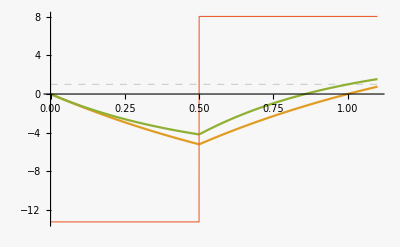
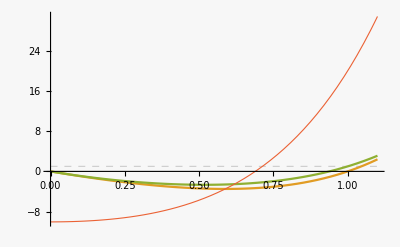
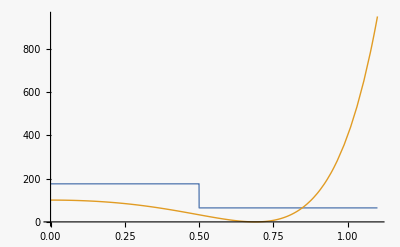

```mathematica
{p1,p2,p2a}
```

```mathematica
{NIntegrate[(uNaive/.usol)^2,{t,0,1}],NIntegrate[uopt^2,{t,0,1}]}
```

{{120.213},74.7884}

Redo for λ=1+δ, and show that effort diverges if goals are not the same.  
(Maybe need to redo to have different goals.)

```mathematica
Φ3=MatrixExp[a t]; Wg3=Integrate[Φ3.b.bᵀ.Φ3ᵀ,{t,0,τ}]; Wginv3=Inverse[Wg3]//Simplify;{MatrixForm[Wg3],MatrixForm[Wginv3]}
```

{(1/2-ⅇ^(-2 τ)/2 | (1-ⅇ^(-((2+δ) τ)))/(2+δ)
(1-ⅇ^(-((2+δ) τ)))/(2+δ) | -(-1+ⅇ^(-2 (1+δ) τ))/(2 (1+δ))),((-1+ⅇ^(-2 (1+δ) τ))/(2 (1+δ) (((1/2-ⅇ^(-2 τ)/2) (-1+ⅇ^(-2 (1+δ) τ)))/(2 (1+δ))+((-1+ⅇ^(-((2+δ) τ)))^2)/(2+δ)^2)) | (1-ⅇ^(-((2+δ) τ)))/((2+δ) (((1/2-ⅇ^(-2 τ)/2) (-1+ⅇ^(-2 (1+δ) τ)))/(2 (1+δ))+((-1+ⅇ^(-((2+δ) τ)))^2)/(2+δ)^2))
(1-ⅇ^(-((2+δ) τ)))/((2+δ) (((1/2-ⅇ^(-2 τ)/2) (-1+ⅇ^(-2 (1+δ) τ)))/(2 (1+δ))+((-1+ⅇ^(-((2+δ) τ)))^2)/(2+δ)^2)) | -(1/2-ⅇ^(-2 τ)/2)/(((1/2-ⅇ^(-2 τ)/2) (-1+ⅇ^(-2 (1+δ) τ)))/(2 (1+δ))+((-1+ⅇ^(-((2+δ) τ)))^2)/(2+δ)^2))}

```mathematica
Det[Wg3]//Simplify//MatrixForm
```

(δ^2+ⅇ^(-2 (2+δ) τ) δ^2+8 ⅇ^(-((2+δ) τ)) (1+δ)-ⅇ^(-2 τ) (2+δ)^2-ⅇ^(-2 (1+δ) τ) (2+δ)^2)/(4 (1+δ) (2+δ)^2)

```mathematica
Series[Det[Wg3],{δ,0,2}]
```

1/16 ⅇ^(-4 τ) (1-2 ⅇ^(2 τ)+ⅇ^(4 τ)-4 ⅇ^(2 τ) τ^2) δ^2+O[δ]^3

```mathematica
Series[Det[Wg3],{τ,0,4}]
```

(δ^2 τ^4)/12+O[τ]^5

```mathematica
Series[Wg3,{τ,0,2}]//Normal//MatrixForm
```

(τ-τ^2 | τ+1/2 (-2-δ) τ^2
τ+1/2 (-2-δ) τ^2 | τ+(-1-δ) τ^2)

```mathematica
uopt3=bᵀ.MatrixExp[a (1-t)].(Wginv3/.τ->1).xtarget//Simplify//Flatten//First; uopt3
```

(2 ⅇ^(1+t+δ) (1+δ) (2+δ) (2-2 ⅇ^(2+δ)-ⅇ^(t δ) (2+δ)+ⅇ^(2+t δ) (2+δ)))/(δ^2+ⅇ^(4+2 δ) δ^2+8 ⅇ^(2+δ) (1+δ)-ⅇ^2 (2+δ)^2-ⅇ^(2+2 δ) (2+δ)^2)

```mathematica
eqs3={x1'[t]+ x1[t]==uopt3,x1[0]==0,x2'[t]+ (1+δ) x2[t]==uopt3,x2[0]==0};
xs3=DSolveValue[eqs3,{x1[t],x2[t]},t]//Simplify
```

{-(2 ⅇ^(1-t+δ) (ⅇ^2-ⅇ^(2 t)-ⅇ^(2+δ)+ⅇ^(t (2+δ))+ⅇ^(2+2 t+δ)-ⅇ^(2+t (2+δ))) (2+3 δ+δ^2))/(δ^2+ⅇ^(4+2 δ) δ^2+8 ⅇ^(2+δ) (1+δ)-ⅇ^2 (2+δ)^2-ⅇ^(2+2 δ) (2+δ)^2),(ⅇ^(-((-1+t) (1+δ))) (δ^2+4 ⅇ^(2+δ) (1+δ)+4 ⅇ^(t (2+δ)) (1+δ)-4 ⅇ^((1+t) (2+δ)) (1+δ)-ⅇ^2 (2+δ)^2-ⅇ^(2 t (1+δ)) (2+δ)^2+ⅇ^(2 (1+t+t δ)) (2+δ)^2))/(δ^2+ⅇ^(4+2 δ) δ^2+8 ⅇ^(2+δ) (1+δ)-ⅇ^2 (2+δ)^2-ⅇ^(2+2 δ) (2+δ)^2)}

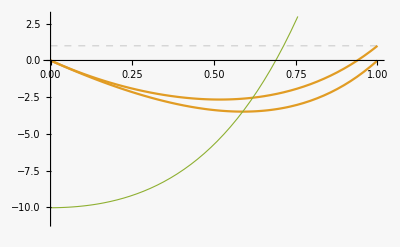

```mathematica
p3=Plot[{1,xs3/.δ->1,uopt3/.δ->1},{t,0,1},PlotStyle->{Directive[Thickness[0.002],GrayLevel[0.8],Dashed],,Thickness[0.002],},PlotRange->{-11,3}]
```

```mathematica
effort[δ0_]:=NIntegrate[uopt3^2/.δ->δ0,{t,0,1}]
```

```mathematica
uopt3s=Series[uopt3,{δ,0,-1}]//Normal
```

(4 ⅇ^(1+t) (-1-ⅇ^2-2 t+2 ⅇ^2 t))/((1-6 ⅇ^2+ⅇ^4) δ)

```mathematica
efforts[δ0_]:=NIntegrate[uopt3s^2/.δ->δ0,{t,0,1}]
```

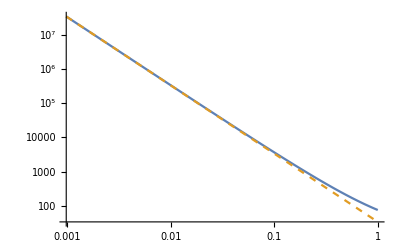

```mathematica
LogLogPlot[{effort[δ],efforts[δ]},{δ,0,1},PlotStyle->{,Dashed}] (* series approximation is good for small δ *)
```

```mathematica
Wgeigs3=Eigenvalues[Wg3]//Simplify;TraditionalForm[Wgeigs3]
```

{1/(4 (δ+1) (δ+2))ⅇ^(-3 (δ+2) τ) (δ^2 ⅇ^(3 (δ+2) τ)-δ^2 ⅇ^((3 δ+4) τ)-√((δ+2)^2 ⅇ^(2 (δ+2) τ) ((δ+1) ⅇ^(2 (δ+1) τ)-(δ+2) ⅇ^(2 (δ+2) τ)+ⅇ^(2 τ))^2-4 (δ+1) ⅇ^(4 (δ+2) τ) (δ^2 ⅇ^(2 (δ+2) τ)+δ^2-(δ+2)^2 ⅇ^(2 τ)-(δ+2)^2 ⅇ^(2 (δ+1) τ)+8 (δ+1) ⅇ^((δ+2) τ)))+4 δ ⅇ^(3 (δ+2) τ)-δ ⅇ^((δ+4) τ)-3 δ ⅇ^((3 δ+4) τ)+4 ⅇ^(3 (δ+2) τ)-2 ⅇ^((δ+4) τ)-2 ⅇ^((3 δ+4) τ)),1/(4 (δ+1) (δ+2))ⅇ^(-3 (δ+2) τ) (δ^2 ⅇ^(3 (δ+2) τ)-δ^2 ⅇ^((3 δ+4) τ)+√((δ+2)^2 ⅇ^(2 (δ+2) τ) ((δ+1) ⅇ^(2 (δ+1) τ)-(δ+2) ⅇ^(2 (δ+2) τ)+ⅇ^(2 τ))^2-4 (δ+1) ⅇ^(4 (δ+2) τ) (δ^2 ⅇ^(2 (δ+2) τ)+δ^2-(δ+2)^2 ⅇ^(2 τ)-(δ+2)^2 ⅇ^(2 (δ+1) τ)+8 (δ+1) ⅇ^((δ+2) τ)))+4 δ ⅇ^(3 (δ+2) τ)-δ ⅇ^((δ+4) τ)-3 δ ⅇ^((3 δ+4) τ)+4 ⅇ^(3 (δ+2) τ)-2 ⅇ^((δ+4) τ)-2 ⅇ^((3 δ+4) τ))}

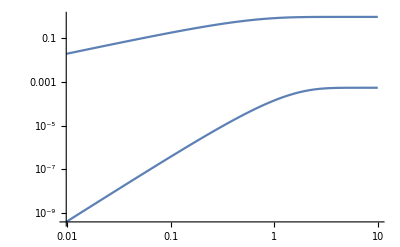

```mathematica
LogLogPlot[Wgeigs3/.δ->0.1,{τ,0,10}]
```

```mathematica
eigratio=Limit[Wgeigs3[[2]]/Wgeigs3[[1]],τ->∞,Assumptions->0<δ<1]//Simplify
```

(4+4 δ+δ^2+√(16+32 δ+20 δ^2+4 δ^3+δ^4))/(4+4 δ+δ^2-√(16+32 δ+20 δ^2+4 δ^3+δ^4))

```mathematica
Series[eigratio,{δ,0,2}]
```

16/δ^2+16/δ+6+(15 δ^2)/16+O[δ]^3

```mathematica
uopt3a=bᵀ.MatrixExp[a (1-t)].(Wginv3).xtarget/.t->s τ//Simplify//Flatten//First; uopt3a
```

(-1/2 ⅇ^(-2 τ+(1+δ) (-1+s τ)) (-1+ⅇ^(2 τ))+(ⅇ^(-1+s τ) (1-ⅇ^(-((2+δ) τ))))/(2+δ))/(((1/2-ⅇ^(-2 τ)/2) (-1+ⅇ^(-2 (1+δ) τ)))/(2 (1+δ))+((-1+ⅇ^(-((2+δ) τ)))^2)/(2+δ)^2)

Long protocols (τ → ∞) are problematic as they require large u in general.  So the control effort is more properly

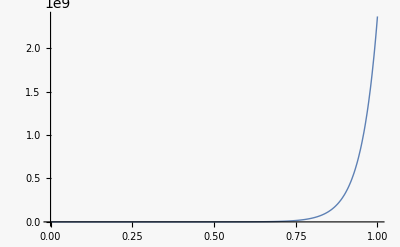

```mathematica
Plot[uopt3a/.{τ->10,δ->1},{s,0,1}]
```

```mathematica
Series[uopt3a,{τ,∞,0}]
```

(ⅇ^((-2+s+s δ) τ+(-1-δ)+O[1/τ]^2))/(2 (-1/(4 (1+δ))+(ⅇ^(-2 τ+O[1/τ]^2))/(4 (1+δ))+(ⅇ^(-2 (1+δ) τ+O[1/τ]^2))/(4 (1+δ))-(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(4 (1+δ))+1/(2+δ)^2-(2 ⅇ^((-2-δ) τ+O[1/τ]^2))/(2+δ)^2+(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(2+δ)^2))-(ⅇ^((s+s δ) τ+(-1-δ)+O[1/τ]^2))/(2 (-1/(4 (1+δ))+(ⅇ^(-2 τ+O[1/τ]^2))/(4 (1+δ))+(ⅇ^(-2 (1+δ) τ+O[1/τ]^2))/(4 (1+δ))-(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(4 (1+δ))+1/(2+δ)^2-(2 ⅇ^((-2-δ) τ+O[1/τ]^2))/(2+δ)^2+(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(2+δ)^2))+(ⅇ^(s τ-1+O[1/τ]^2))/((2+δ) (-1/(4 (1+δ))+(ⅇ^(-2 τ+O[1/τ]^2))/(4 (1+δ))+(ⅇ^(-2 (1+δ) τ+O[1/τ]^2))/(4 (1+δ))-(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(4 (1+δ))+1/(2+δ)^2-(2 ⅇ^((-2-δ) τ+O[1/τ]^2))/(2+δ)^2+(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(2+δ)^2))-(ⅇ^((-2+s-δ) τ-1+O[1/τ]^2))/((2+δ) (-1/(4 (1+δ))+(ⅇ^(-2 τ+O[1/τ]^2))/(4 (1+δ))+(ⅇ^(-2 (1+δ) τ+O[1/τ]^2))/(4 (1+δ))-(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(4 (1+δ))+1/(2+δ)^2-(2 ⅇ^((-2-δ) τ+O[1/τ]^2))/(2+δ)^2+(ⅇ^(-2 (2+δ) τ+O[1/τ]^2))/(2+δ)^2))

Export data (trajectories and input signals for different δ values)

```mathematica
Δt=0.01;
datx1=(xs3/.δ->1/.t->Range[0,1,Δt])ᵀ//N;
datu1=uopt3/.δ->1/.t->Range[0,1,Δt]//N;
datx2=(xs3/.δ->0.5/.t->Range[0,1,Δt])ᵀ//N;
datu2=uopt3/.δ->0.5/.t->Range[0,1,Δt]//N;

alldata=Join[datx1,{datu1}ᵀ,datx2,{datu2}ᵀ,2]   (* concatenates columns *);
(* 
SetDirectory[NotebookDirectory[]];
Export["nearlyIdentical.dat",alldata];
*)
```